## Load data so we can get tid string

```mathematica
fName="20180817-orb_1607-densPA_45-sRate0_63-Mathematica.csv";
```

```mathematica
inDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/txtOutput/";
Options[loadJVCSV]={printFName->False};
loadJVCSV[OptionsPattern[]]:=Module[{},
If[OptionValue[printFName],Print[fName]];(*
data=Cases[Import[inDir<>fName,"Table"],{_?NumberQ,___}];
data=Cases[Import[inDir<>fName,"Table"],{_?StringQ,___}]*)
data=Import[inDir<>fName,{"CSV","Data"},"HeaderLines"-> 1]
]
```

Header line

```mathematica
Import[inDir<>fName,{"Data",1,All}]//TableForm[#,TableDirections->Row]&
```

Tid | pot | potErr | cur | curErr | je | jeerr | nDown | nDownErr | downEpot | downEpotErr

Load variables

```mathematica
data=loadJVCSV[];
```

```mathematica
{tids,pots,potErrs,curs,curErrs,jes,jeErrs,dens,densErrs,densPots,densPotErrs}=data[[All,#]]&/@Range[1,11];
```

### Select times/indices

```mathematica
interval=2;
```

```mathematica
itvlTidStr=Switch[interval,
1,
{{"12:00:28.5","12:00:38.7"},{"12:00:40.0","12:00:48"}},
2,
{"01:04:28.5","01:04:41"} ;
Switch[fName,
"20180817-orb_1607-densPA_45-sRate0_63-Mathematica.csv",
{"01:04:29.3","01:04:40.5"},
"20180817-orb_1607-densPA_45-sRate1_89-Mathematica.csv",
{"01:04:29.3","01:04:41.5"},
"20180817-orb_1607-densPA_45-sRate0_31-Mathematica.csv",
{"01:04:29.3","01:04:41.5"}]
];
```

```mathematica
itvlBounds=Switch[Length@Dimensions[itvlTidStr],
1,
Flatten@((minTidInd[#,tids])&/@itvlTidStr),
2,

{Flatten@((minTidInd[#,tids])&/@itvlTidStr[[1,;;]]),Flatten@((minTidInd[#,tids])&/@itvlTidStr[[2,;;]])}
];
```

```mathematica
tids[[#]]&/@itvlBounds
```

{01:04:28.695,01:04:40.055}

```mathematica
inds1=Switch[Length@Dimensions[itvlTidStr],
1,
Range@@itvlBounds,
2,
Flatten[{Range@@itvlBounds[[1,;;]],Range@@itvlBounds[[2,;;]]}]
];
```

```mathematica
tid=tids[[inds1]];
```

## Load other things

```mathematica
nTrials=1000;
```

```mathematica
SetDirectory["/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180815/"]
```

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180815/Orb4682

```mathematica
kFiles=FileNames[RegularExpression["Orb1607_itvl2_kappa-fixT90eV.*nVJVJeV(-\\d\\d)?.wdx"]]
```

{Orb4682_itvl2_kappa-fixT110eV_nRolls200_nVJVJeV-01.wdx,Orb4682_itvl2_kappa-fixT110eV_nRolls200_nVJVJeV.wdx,Orb4682_itvl2_kappa-fixT110eV_nRolls600_nVJVJeV.wdx}

```mathematica
gFiles=FileNames[RegularExpression["Orb1607_itvl2_Maxwell-fixT70eV.*nVJVJeV(-\\d\\d)?.wdx"]]
```

{Orb4682_itvl2_Maxwell-fixT96eV_nRolls1000_nVJVJeV.wdx}

RESTORE DATA FILES

```mathematica
For[i=1,i≤ Length@kFiles,i++,
Print[kFiles[[i]]];
If[FileExistsQ[kFiles[[i]]],
Print[Ja];
<<(kFiles[[i]]);
If[i==1,
kMCValsMaster=((kFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};,
kMCVals=((kFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};
kMCValsMaster = Transpose[(Transpose[kMCValsMaster]~Join~Transpose[kMCVals])];
];
];
]
```

Orb4682_itvl2_kappa-fixT110eV_nRolls200_nVJVJeV-01.wdx

Ja

Orb4682_itvl2_kappa-fixT110eV_nRolls200_nVJVJeV.wdx

Ja

Orb4682_itvl2_kappa-fixT110eV_nRolls600_nVJVJeV.wdx

Ja

```mathematica
For[i=1,i≤ Length@gFiles,i++,
Print[gFiles[[i]]];
If[FileExistsQ[gFiles[[i]]],
Print[Ja];
<<(gFiles[[i]]);
If[i==1,
gMCValsMaster=((gFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};,
gMCVals=((gFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};
gMCValsMaster = Transpose[(Transpose[gMCValsMaster]~Join~Transpose[gMCVals])];
];
];
]
```

Orb4682_itvl2_Maxwell-fixT96eV_nRolls1000_nVJVJeV.wdx

Ja

```mathematica
kMCValsMaster//Dimensions
```

{4,1000}

```mathematica
gMCValsMaster//Dimensions
```

{4,1000}

```mathematica
kMCVals=kMCValsMaster;
gMCVals=gMCValsMaster;
Clear[kMCValsMaster,gMCValsMaster];
```

## Plots!

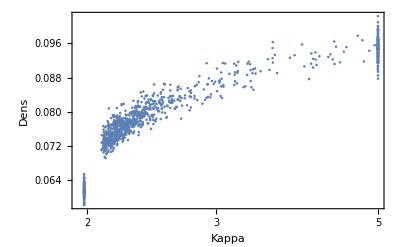

```mathematica
ListLogLinearPlot[Partition[Riffle[kMCVals[[4,;;]],kMCVals[[1,;;]]],2],Frame->True,FrameLabel->{"Kappa","Dens"}]
```

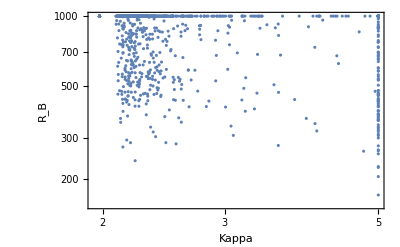

```mathematica
ListLogLogPlot[Partition[Riffle[kMCVals[[4,;;]],kMCVals[[3,;;]]],2],Frame->True,FrameLabel->{"Kappa","R_B"}]
```

```mathematica
kMCTitles={"N (cm^-3)","T (eV)","R_B","κ"};
kMCPDFTitles={"PDF (cm^3)","PDF (eV^-1)","PDF (R_B^-1)","PDF (κ^-1)"};
gMCTitles={"N (cm^-3)","T (eV)","R_B"};
```

```mathematica
binSizes=Table[Automatic,4];
```

```mathematica
binSizes={{0.005},{0.2},{100},{0.2}};
```

```mathematica
MCTitle=StringJoin@Riffle[tid[[{1,-1}]],"–"];
```

```mathematica
densPlotRange:={{2.2,3.2},{0.01,0.2}};
```

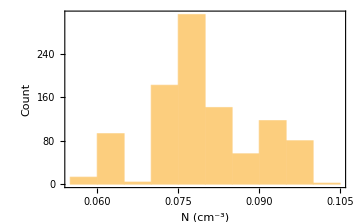
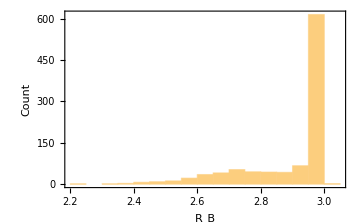
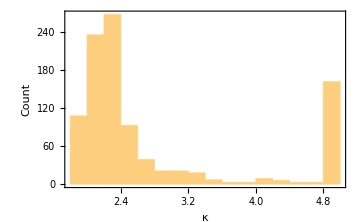
-Graphics--Graphics--Graphics--Graphics-

```mathematica
kHistosPlot=Row[Table[Histogram[If[MCParmInd==3,Log10[kMCVals[[MCParmInd]]],kMCVals[[MCParmInd]]],If[MCParmInd==3,Automatic,binSizes[[MCParmInd]]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

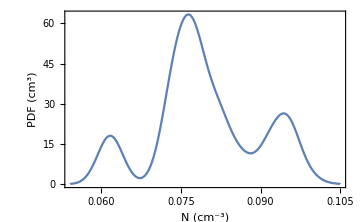
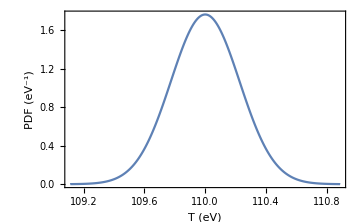
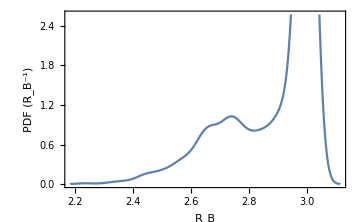
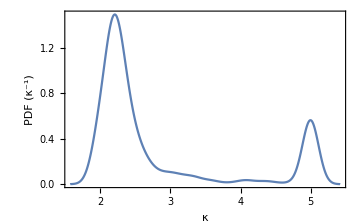

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[If[MCParmInd≠ 3,kMCVals[[MCParmInd]],Log10[kMCVals[[MCParmInd]]]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

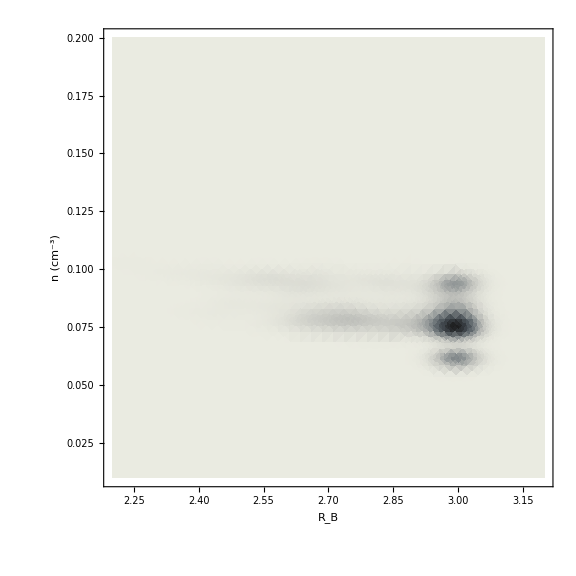

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[Log10[kMCVals[[3]]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

Maxwellian plots

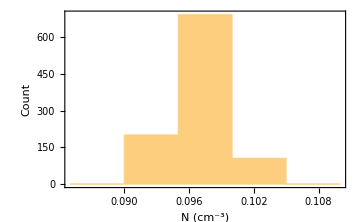
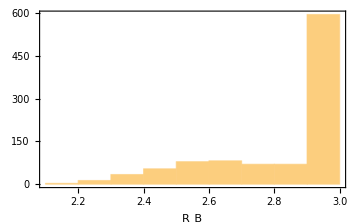
-Graphics--Graphics--Graphics-

```mathematica
Row[Table[Histogram[If[MCParmInd≠ 3,gMCVals[[MCParmInd]],Log10[gMCVals[[MCParmInd]]]],If[MCParmInd≠ 3,binSizes[[MCParmInd]],Automatic],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

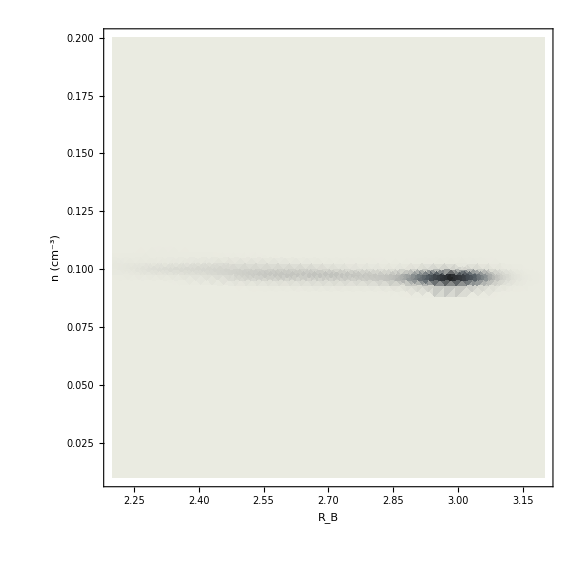

```mathematica
SmoothDensityHistogram[Partition[Riffle[Log10[gMCVals[[3]]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```